# Learning Mathematica

## Vitor Abreu de Carvalho DRE: 121077657

## Observações

- Os comandos do Mathematica sempre começam com letras maiúsculas.

## Comandos Básicos

### Edição de Texto

- Aumentar a fonte do texto: “alt” + “=”
- Diminuir a fonte do texto: “alt” + “-“

### Codificação

Atribuição de Variáveis

```mathematica
a = 3
b = 5;
```

3

### Funções e Gráficos

```mathematica
Quit
```

## Definindo f(x)

```mathematica
f[x_]:= x^(2) ;
```

```mathematica
f[2]
```

4

```mathematica
f[4]
```

16

```mathematica
f[f[2]]
```

16

Plotagem do Gráfico da função

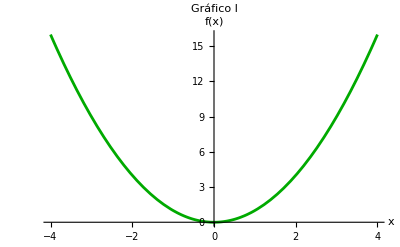

```mathematica
p1 = Plot[f[x],{x,-4,4},AxesLabel->{"x","f(x)"},PlotStyle->Darker[Green],PlotLabel->"Gráfico I"]
```

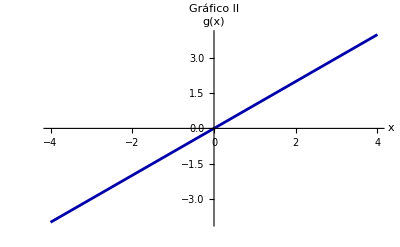

```mathematica
g[x_] := x;
p2 = Plot[g[x], {x,-4,4},AxesLabel->{"x","g(x)"},PlotStyle->Darker[Blue],PlotLabel->"Gráfico II"]
```

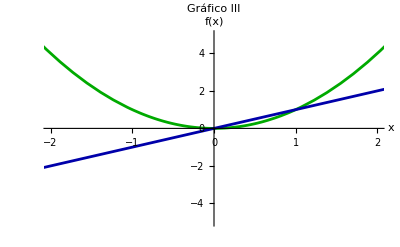

```mathematica
Show[p1,p2, PlotRange -> {{-2,2},{-5,5}}, AxesLabel -> {"x", "f(x)"}, PlotLabel -> Gráfico III]
```

## Gráficos com parâmetros Variáveis [Manipulate]

```mathematica
Manipulate[Plot[x^(n),{x, 0,10}], {n,1,5}]
```

```mathematica
Manipulate[Plot[x^(n)+ m,{x,0,10}, PlotStyle->Darker[Green]], {n,1,5}, {m,0,5}]
```

```mathematica
Manipulate[Plot[x^(n)+ m,{x,0,10}, PlotStyle->Darker[Green], Frame-> foto], {{n,1,"Potência"},1,5}, {{m,0,"Eixo y"},0,5},{foto, {True, False}}]
```

## Listas

```mathematica
List[a,b,c]
```

{a,b,c}

```mathematica
{d,e,f,g,h}
```

{d,e,f,g,h}

```mathematica
lista = List[a,b,c]
lista1 = {d,e,f,g,h}
```

{a,b,c}

{d,e,f,g,h}

```mathematica
Length[lista1]
```

5

```mathematica
lista[[1]]
```

a

```mathematica
Append[lista1,"Vitor"]
```

```mathematica
{d,e,f,g,h,"Vitor"}
```

{d,e,f,g,h,Vitor}

```mathematica
lista1
```

{d,e,f,g,h}

```mathematica
lista3 = Append[lista1,"Vitor"]
```

{d,e,f,g,h,Vitor}

```mathematica
lista3
```

{d,e,f,g,h,Vitor}

```mathematica
lista11 = {{a,b,c},d,e,f}
```

{{a,b,c},d,e,f}

```mathematica
lista11[ [1,2] ]
```

b

```mathematica
lista11 [ [3] ]
```

e

## Tabelas

```mathematica
Table[3,2]
```

{3,3}

```mathematica
Table[3i,{i,1,5}]
```

{3,6,9,12,15}

```mathematica
Table[3i,{i,1,5,2}]
```

{3,9,15}

```mathematica
Table[3i,{i,{1,4,9,55}}]
```

{3,12,27,165}

```mathematica
Table[N[Sin[i]],{i,0, Pi,Pi/2}]
```

{0.,1.,0.}

N representa o valor nu.08mérico, obrigando o valor em colchetes, neste caso o seno, a ser calculado.

```mathematica
Table[3i + j,{i,1,3},{j,1,3}]
```

{{4,5,6},{7,8,9},{10,11,12}}

Ideia interessante para criar pontos num gráfico ***********************************************************************************************

```mathematica
MatrixForm[%]
```

(4 | 5 | 6
7 | 8 | 9
10 | 11 | 12)

% Indica que é a última coisa que rodamos no código

## Solucionando Equações

```mathematica
Solve [x^(2)+1 == 0]
```

{{x→-ⅈ},{x→ⅈ}}

```mathematica
Solve[a + b + c == 1, a]
```

{{a→1-b-c}}

Isolamos o parâmetro a na equação

```mathematica
Solve[x^(2) + 8x + 1 == 0, Integers]
```

{}

Solução apenas para valores inteiros

```mathematica
Solve[x^(2) + 8x + 1 == 0, Reals]
```

{{x→-4-√15},{x→-4+√15}}

Solução para valores Reais

```mathematica
SolveAlways[a x^(2) + b == 0, x]
```

{{a→0,b→0}}

Retorna os valores dos parâmetros de forma que a eq. seja válida para todos os valores reais

```mathematica
NSolve[x^(2) + x^(3) - x^(4) == -1]
```

{{x→-1.},{x→0.122561-0.744862 ⅈ},{x→0.122561+0.744862 ⅈ},{x→1.75488}}

```mathematica
NSolve[x^(2) + x^(3) - x^(4) == -1, Reals]
```

{{x→-1.},{x→1.75488}}

## Criando Gráficos a partir de Listas

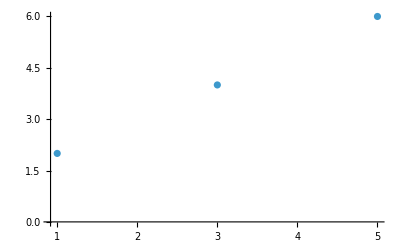

```mathematica
lista1 = {{1,2},{3,4},{5,6}};
plot1 = ListPlot[lista1]
```

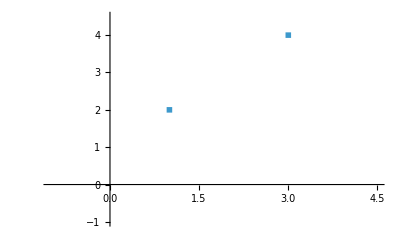

```mathematica
plot2 = ListPlot[lista1, PlotMarkers-> ■, PlotRange->{{-1,4.5},{-1,4.5}}]
```

Modificando marcador, link para escolha dos tipos de marcadores: https://reference.wolfram.com/language/guide/ShapesIconsAndRelatedCharacters.html

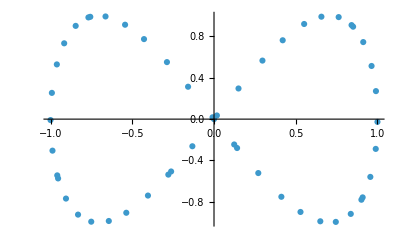

```mathematica
plot3 = ListPlot[Table[{Sin[n],Sin[2n]},{n, 0, 50}]]
```

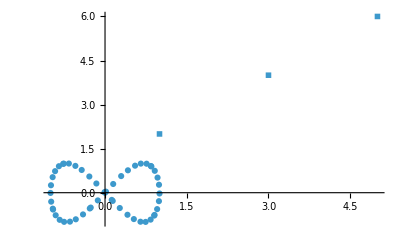

```mathematica
Show[plot2,plot3,PlotRange -> All]
```

## Estruturas de Repetição

While | If | Do

```mathematica
j = 1;
While [j <= 4, Print[j^2]; j = j + 1]
```

1

4

9

16

```mathematica
a = 3;
If[a == 4, Print["a = 4"], Print["a=", a]]
```

a=3

```mathematica
Do[Print[2^(i)],{i,1,5}]
```

2

4

8

16

32

```mathematica
Do[Print[2^(i)],{i,1,10,2}]
```

2

8

32

128

512

Está com passo 2

```mathematica
Do[Print[2^(i)],{i,{1,10,100}}]
```

2

1024

1267650600228229401496703205376

Está usando valores específicos para o i

```mathematica
Do[Print[2^(i + j)], {i,1,2},{j,1,2}]
```

4

8

8

16

```mathematica
Clear [j]
```

Limpando a variável

```mathematica
j = 10;
If[j <5 , Do[Print[j^(i)],{i,1,5}], Do[Print[j^(5*i)],{i,1,5}]]
```

100000

10000000000

1000000000000000

100000000000000000000

10000000000000000000000000